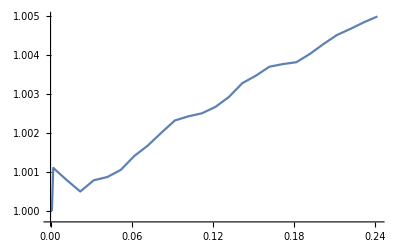

```mathematica
imported =Import[FileNameJoin[{NotebookDirectory[],"output.json"}]];
T="time"/.imported;
V="volume"/.imported;
ListPlot[Transpose[{T,V/V[[1]]}],Joined->True]
```